```mathematica
fFunc[r0_,r1_,r2_,T_] = r0^T/(r0^T+r1^T+r2^T)
FullSimplify[D[fFunc[r0,r1,r2,T],r0]^2*r0+D[fFunc[r0,r1,r2,T],r1]^2*r1+D[fFunc[r0,r1,r2,T],r2]^2*r2]
```

r0^T/(r0^T+r1^T+r2^T)

(r0^(-1+2 T) (r1 r2 (r1^T+r2^T)^2+r0 (r1^(2 T) r2+r1 r2^(2 T))) T^2)/(r1 r2 (r0^T+r1^T+r2^T)^4)

```mathematica
fFunc[r0,r1,r2,Ttarg]
```

r0^Ttarg/(r0^Ttarg+r1^Ttarg+r2^Ttarg)

```mathematica
Solve[fFunc[r0,r1,r2,Ttarg]*alpha+beta-r0T/nTarg==0,beta]
```

{{beta→r0T/nTarg-(alpha r0^Ttarg)/(r0^Ttarg+r1^Ttarg+r2^Ttarg)}}

```mathematica
FullSimplify[D[r0Func,r0]^2*r0+D[r0Func,r1]^2*r1+D[r0Func,r2]^2*r2]
```

(alpha^2 nTarg^2 r0^(-1+2 Ttarg) (r1 r2 (r1^Ttarg+r2^Ttarg)^2+r0 (r1^(2 Ttarg) r2+r1 r2^(2 Ttarg))) Ttarg^2)/(r1 r2 (r0^Ttarg+r1^Ttarg+r2^Ttarg)^4)

```mathematica
D[%26[[1,1,2]],alpha]==0
```

(alpha r0^(2 Ttarg) (r1T+r2T))/((-r0^Ttarg+alpha r0^Ttarg-r1^Ttarg-r2^Ttarg)^2)-(r0^Ttarg (r1T+r2T))/(-r0^Ttarg+alpha r0^Ttarg-r1^Ttarg-r2^Ttarg)==0

```mathematica
fFunc[r0,r1,r2,Ttarg]*alpha
```

(alpha r0^Ttarg)/(r0^Ttarg+r1^Ttarg+r2^Ttarg)

WolframAlphaQueryResults

```mathematica
Sum[1/Factorial[k]^beta,{k,0,Infinity},Assumptions->beta>0]
```

Sum[(k!)^-beta,{k,0,∞},Assumptions→beta>0]

```mathematica
Integrate[Exp[-x^6/(2*sigma^6)],{x,-Infinity,Infinity},Assumptions->sigma>0]
```

2 2^(1/6) sigma Gamma[7/6]

```mathematica
Log[Exp[-x^6/(2*2^6)]+5*Exp[-x^6/(2*1^6)]]
```

Log[5 ⅇ^(-x^6/2)+ⅇ^(-x^6/128)]

```mathematica
CakeFunc[width_,exponent_,amp_,ndim_,r_] = Sqrt[(Gamma[ndim]^2/2^(ndim-2))]*ndim*1/Gamma[(ndim+1)/2]*Sqrt[Pi]/(2*2^(ndim/exponent)*width^ndim*Gamma[(exponent+ndim)/exponent]*Sqrt[(2*Pi)^ndim])*amp*Exp[-r^exponent/(2*width^exponent)]
```

```mathematica
Integrate[amp2*Exp[-x^(2*n)/(2*width2^(2*n))],{x,-Infinity,Infinity},Assumptions->width2>0&&Element[n,Integers]&&n>0]
```

$Aborted

```mathematica
FullSimplify[Sqrt[(Gamma[ndim]^2/2^(ndim-2))]*ndim*1/Gamma[(ndim+1)/2]*Sqrt[Pi]/(2*2^(ndim/(exponent))*width^ndim*Gamma[(exponent+ndim)/(exponent)]*Sqrt[(2*Pi)^ndim]),Element[ndim,Integers]&&ndim≥1&&Element[exponent,Integers]&&exponent≥1]
```

(2^(-ndim/exponent) π^(-ndim/2) width^-ndim Gamma[1+ndim/2])/Gamma[(exponent+ndim)/exponent]

```mathematica
CakeFunc[width_,exponent_,amp_,ndim_,r_] = Gamma[1+ndim/2]/(2^(ndim/exponent)*Pi^(ndim/2)*width^ndim*Gamma[(exponent+ndim)/exponent])*amp*Exp[-r^exponent/(2*width^exponent)]
```

(2^(-ndim/exponent) amp ⅇ^(-1/2 r^exponent width^-exponent) π^(-ndim/2) width^-ndim Gamma[1+ndim/2])/Gamma[(exponent+ndim)/exponent]

```mathematica
FullSimplify[Integrate[2*CakeFunc[width1,6,1,x]*x,{x,0,Infinity},Assumptions->width1>0]]
```

(width1 Gamma[2/3])/(√(2 π))

```mathematica
{1,11/10},{2,12/10},{4,14/10}
```

```mathematica
Gamma[(5+1)/2]
```

2

```mathematica
exploc = 8;
Integrate[CakeFunc[width1,exploc,1,1,Sqrt[x^2]],{x,-Infinity,Infinity},Assumptions->width1>0]
Integrate[CakeFunc[width1,exploc,1,2,Sqrt[x^2+y^2]],{x,-Infinity,Infinity},{y,-Infinity,Infinity},Assumptions->width1>0]
Integrate[CakeFunc[width1,exploc,1,3,Sqrt[x^2+y^2+z^2]],{x,-Infinity,Infinity},{y,-Infinity,Infinity},{z,-Infinity,Infinity},Assumptions->width1>0]
Integrate[CakeFunc[width1,exploc,1,4,Sqrt[x^2+y^2+z^2+w^2]],{x,-Infinity,Infinity},{y,-Infinity,Infinity},{z,-Infinity,Infinity},{w,-Infinity,Infinity},Assumptions->width1>0]
Integrate[CakeFunc[width1,exploc,1,5,Sqrt[x^2+y^2+z^2+w^2+t^2]],{x,-Infinity,Infinity},{y,-Infinity,Infinity},{z,-Infinity,Infinity},{w,-Infinity,Infinity},{t,-Infinity,Infinity},Assumptions->width1>0]
Integrate[CakeFunc[width1,exploc,1,6,Sqrt[x^2+y^2+z^2+w^2+t^2+b^2]],{x,-Infinity,Infinity},{y,-Infinity,Infinity},{z,-Infinity,Infinity},{w,-Infinity,Infinity},{t,-Infinity,Infinity},{b,-Infinity,Infinity},Assumptions->width1>0]
Integrate[CakeFunc[width1,exploc,1,7,Sqrt[x^2+y^2+z^2+w^2+t^2+b^2+c^2]],{x,-Infinity,Infinity},{y,-Infinity,Infinity},{z,-Infinity,Infinity},{w,-Infinity,Infinity},{t,-Infinity,Infinity},{b,-Infinity,Infinity},{c,-Infinity,Infinity},Assumptions->width1>0]
```

1

1

1

«4 more identical outputs»

```mathematica
{1/2,1,1/2,1/9,1/(6*Sqrt[2])^2,1/30^2,1/(90*Sqrt[2])^2}
```

{1/2,1,1/2,1/9,1/72,1/900,1/16200}

```mathematica
Table[1/(Gamma[n]^2/2^(n-2)),{n,1,7}]
```

{1/2,1,1/2,1/9,1/72,1/900,1/16200}

```mathematica
Gamma[1/2]
```

√π

```mathematica
tier1 = Integrate[CakeFunc[width1,8,1,x],{x,-Infinity,Infinity},Assumptions->width1>0]
(*tier1 = 1/(2*2^(1/8)*width1*Gamma[9/8])*Integrate[amp1*Exp[-x^8/(2*width1^8)],{x,-Infinity,Infinity},Assumptions->width1>0&&Element[n,Integers]&&n>0]*)
tier2 = 1/(2*2^(1/6)*width2*Gamma[7/6])*Integrate[amp2*Exp[-x^6/(2*width2^6)],{x,-Infinity,Infinity},Assumptions->width2>0&&Element[n,Integers]&&n>0]
```

1

amp2

```mathematica
N[Gamma[7/6]]
```

0.927719

```mathematica
tier1/.width1->4
tier2/.width2->0.1
```

amp1

amp2

```mathematica
Integrate[CakeFunc[4,8,1,1,x]+CakeFunc[1/10,6,1,1,x],{x,-6.,6.}]
```

2.

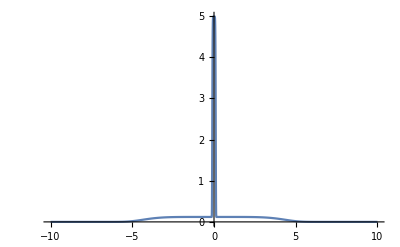

```mathematica
Plot[CakeFunc[4.,6,1,1,x]+CakeFunc[0.1,8,1,1,x],{x,-10,10},PlotRange->All]
```

```mathematica
Plot3D[Exp[-Sqrt[x^2+y^2]^8],{x,-10,10},{y,-10,10},PlotRange->All]
```

-Graphics3D-

```mathematica
FullSimplify[Log[1-Exp[-width^5/(r+r0)^5]],r>0&&r0>0&&width>0]
```

Log[1-ⅇ^(-width^5/(r+r0)^5)]

```mathematica
Integrate[(CakeFunc[4.,6,1,1,r]+CakeFunc[0.1,8,1,1,r])^(1/100),{r,-Infinity,Infinity}]
```

$Aborted

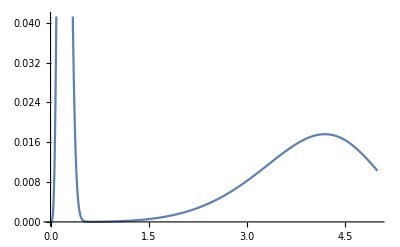

```mathematica
Plot[(CakeFunc[4.,6,1,5,r]+CakeFunc[0.1,2,1,5,r])*r^4,{r,0,5}]
```

```mathematica
RevolutionPlot3D[(CakeFunc[4.,6,1,2,r]+CakeFunc[0.1,2,1,2,r]),{r,0,5},PlotRange->All]
```

-Graphics3D-